```mathematica
(*Quit[]*)
```

# n pi spectral functions

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
<<MyPackages`HistV2`
```

```mathematica
<<"funcs.m"
```

## τ[P]→ ν_τ[k]e[k1]ν_e[k2]

```mathematica
ClearScalarProducts[];
ScalarProduct[q,q]=q2;
(* P -> k q *)
ScalarProduct[P,P]=mTau^2; ScalarProduct[k,k]=0; 
ScalarProduct[P,k]=Calc[(SP[P]+SP[k]-SP[q])/2];
ScalarProduct[P,q]=Calc[(SP[P]+SP[q]-SP[k])/2];
ScalarProduct[k,q]=Calc[(SP[P]-SP[k]-SP[q])/2];
(* q -> k1 k2 *)
ScalarProduct[k1,k1]=0; ScalarProduct[k2,k2]=0;
ScalarProduct[q,k1] = Calc[(SP[q]+SP[k1]-SP[k2])/2];
ScalarProduct[q,k2]=Calc[(SP[q]+SP[k2]-SP[k1])/2];
ScalarProduct[k1,k2]=Calc[(SP[q]-SP[k1]-SP[k2])/2];
Calc[SP[#]]&/@{P,k,k1,k2,q, P-k, k1+k2}
```

{mTau^2,0,0,0,q2,q2,q2}

```mathematica
(* τ -> ν W *)
H = SpinorUBar[k].GA[μ].(1+GA[5]).SpinorU[P, mTau]//FCI;
H2 = H*ComplexConjugate[H/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]}]//FermionSpinSum//ReplaceAll[#,DiracTrace->TR]&;
H2T =Simplify[ Contract[(FV[q,μ]FV[q,ci[μ]]-SP[q]MT[μ,ci[μ]])H2]]
```

4 (mTau^2 q2+mTau^4-2 q2^2)

```mathematica
(* W -> e νe *)
matr = SpinorUBar[k1].GA[μ].(1+GA[5]).SpinorU[k2]//FCI;
matr2 = matr*ComplexConjugate[matr/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]}]//FermionSpinSum//ReplaceAll[#, DiracTrace->TR]&;
rhoT["eν"] =1/(3 q2^2)1/(2π)1/(8π) Calc[(FV[q,μ]FV[q,ci[μ]]-SP[q]MT[μ,ci[μ]])matr2]
```

1/(6 π^2)

```mathematica
Integrate[1/2 1/(2mTau)(1-q2/mTau^2)/(8π)GF^2/2 H2T rhoT["eν"], {q2, 0, mTau^2}]
```

(GF^2 mTau^5)/(192 π^3)

```mathematica
H2T
```

4 (mTau^2 q2+mTau^4-2 q2^2)

## Spectral Functions

```mathematica
Clear[calcHist];
calcHist::usage = "calcHist[hist, \"1+X/(X+Y)\"";
calcHist[hist_,formula_, opts___]:=Module[{
$Y=hist, $X=HST2D[Transpose[{hist⟦1,;;,1⟧,hist⟦1,;;,1⟧}]],
out
},
out = ToExpression[formula]/.{X->$X, Y->$Y};
If[NumericQ[out],out -> $X*out];
out
]
Clear[IdHST];
IdHST[hist_]:=HST2D[Transpose[{hist⟦1,;;,1⟧,hist⟦1,;;,1⟧}]]
```

```mathematica
Clear[dGammaTau, dBrTau];
dGammaTau[mode_]:=1/2 1/(2mTau)(1-q2/mTau^2)/(8π)GF^2/2 H2T rhoT[mode]/.{q2->IdHST[rhoT[mode]]};
dBrTau[mode_]:=1/Γτ dGammaTau[mode];
```

```mathematica
GeV=1.; MeV=10^-3 GeV;
mTau = 1776.86MeV;
GF = 1.166*10^-5 GeV^2;
Γτ=(6.582*10^-25)/(2.9*10^-13);
```

```mathematica
(* checkig τ->eνν *)
IntegralHST[dGammaTau["eν"]]/Γτ/0.1739
```

0.933429

## 2π

⟨ [0.141019;7.97295],  89 entries⟩

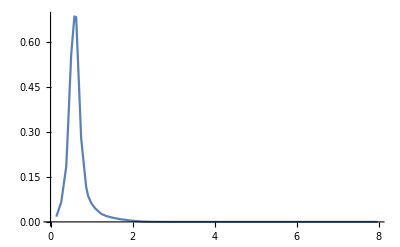

Br[τ->2pi]=25.49 %

```mathematica
out = "chi_c0";
mode = "2pi";
rootP = readROOT[getFileName[out, mode, "1"], Norm ->1];
rootENU = readROOT[getFileName[out, "enu", "1"], Norm ->1];
Quiet[rrr =rootP/rootENU];
rhoT[mode] = HST2D[Select[rrr⟦1⟧,0<#⟦1⟧<mTau^2 &&#⟦2⟧>0&]];
q2 = IdHST[rhoT[mode]];
rhoT[mode] *= 0.2549/IntegralHST[dBrTau[mode]];
rhoT[mode]=HST2D[Join[rhoT[mode]⟦1⟧,Table[{qq,0},{qq,1.1*mTau^2, 8, 0.1}]]]
Clear[q2]
PlotHST[dBrTau[mode], Joined->True, PlotRange->All]
Print["Br[τ->",mode,"]=", 100*IntegralHST[dBrTau[mode]]," %"]
Clear[q2];
```

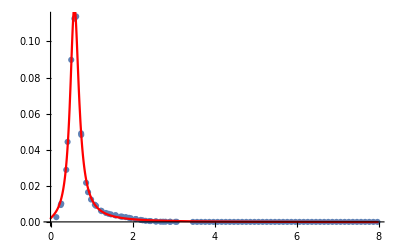

```mathematica
func = (a0+a1 q2+a2 a2^2)/((√q2-M0^2)^2+G^2);
model = NonlinearModelFit[rhoT[mode]⟦1⟧, func,{a0, a1, a2, M0, G},q2];
Show[
PlotHST[rhoT[mode], PlotRange->All],
Plot[model[q2], {q2, 0, 8}, PlotRange->All, PlotStyle->Red]
]
fitRhoT[mode]=model["BestFit"];
```

## 3π

```mathematica
out = "chi_c0";
mode = "3pi";
rootP = readROOT[getFileName[out, mode, "1"], Norm ->1];
rootENU = readROOT[getFileName[out, "enu", "1"], Norm ->1];
Quiet[rrr =rootP/rootENU];
rhoT[mode] = HST2D[Select[rrr⟦1⟧,#⟦2⟧>0&]];
q2 = IdHST[rhoT[mode]];
rhoT[mode] *=9.31*10^-2/IntegralHST[dBrTau[mode]];
Clear[q2]
```

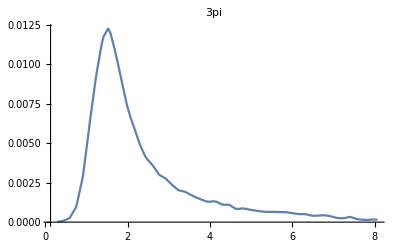

Br[τ->3pi]=9.31 %

```mathematica
PlotHST[rhoT[mode], Joined->True, PlotRange->All, PlotLabel->mode]
Print["Br[τ->",mode,"]=", 100*IntegralHST[dBrTau[mode]]," %"]
```

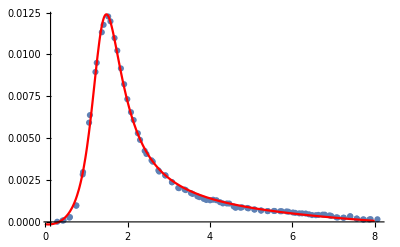

```mathematica
func = (a0+a1 q2+a2 q2^2)/((√q2-M0^2)^2+G^2);
model = NonlinearModelFit[rhoT[mode]⟦1⟧, func,{a0, a1, a2, M0, G},q2];
Show[
PlotHST[rhoT[mode], PlotRange->All],
Plot[model[q2], {q2, 0, 8}, PlotRange->All, PlotStyle->Red]
]
fitRhoT[mode]=model["BestFit"];
```

## 4π

⟨ [0.;7.22563],  104 entries⟩

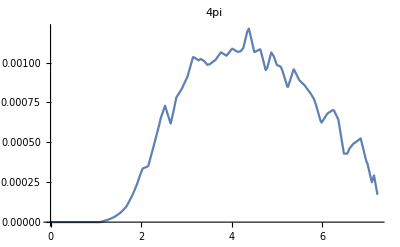

Br[τ->4pi]=4.49 %

```mathematica
out = "chi_c2";
mode = "4pi";
rootP = readROOT[getFileName[out, mode, "1"], Norm ->1];
rootENU = readROOT[getFileName[out, "enu", "1"], Norm ->1];
Quiet[rrr =rootP/rootENU];
rhoT[mode] = HST2D[Select[rrr⟦1⟧,#⟦2⟧>0&]];
rhoT[mode]=HST2D[Join[
Table[{qq,0},{qq,0, 1.1, 0.1}], rhoT[mode]⟦1⟧
]]
q2 = IdHST[rhoT[mode]];
rhoT[mode] *=4.49*10^-2/IntegralHST[dBrTau[mode]];
Clear[q2]
PlotHST[rhoT[mode], Joined->True, PlotRange->All, PlotLabel->mode]
Print["Br[τ->",mode,"]=", 100*IntegralHST[dBrTau[mode]]," %"]
```

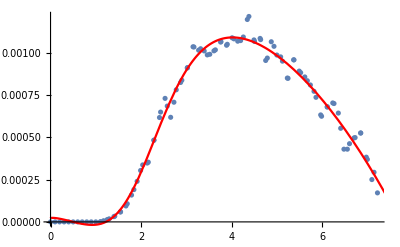

```mathematica
func = (a0+a1 q2+a2 q2^2+a4 q2^4)/((√q2-M0^2)^2+G^2);
model = NonlinearModelFit[rhoT[mode]⟦1⟧, func,{a0, a1, a2, a4, M0, G},q2];
Show[
PlotHST[rhoT[mode], PlotRange->All],
Plot[model[q2], {q2, 0, 8}, PlotRange->All, PlotStyle->Red]
]
fitRhoT[mode]=model["BestFit"];
```

## 5π

⟨ [0.;7.90142],  101 entries⟩

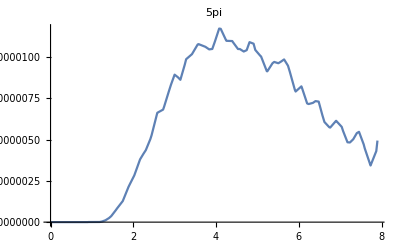

Br[τ->5pi]=0.0775 %

```mathematica
out = "chi_c0";
mode = "5pi";
rootP = readROOT[getFileName[out, mode, "1"], Norm ->1];
rootENU = readROOT[getFileName[out, "enu", "1"], Norm ->1];
Quiet[rrr =rootP/rootENU];
rhoT[mode] = HST2D[Select[rrr⟦1⟧,#⟦2⟧>0&]];
rhoT[mode]=HST2D[Join[
Table[{qq,0},{qq,0, 0.9, 0.1}], rhoT[mode]⟦1⟧
]]
q2 = IdHST[rhoT[mode]];
rhoT[mode] *=7.75*10^-4/IntegralHST[dBrTau[mode]];
Clear[q2]
PlotHST[rhoT[mode], Joined->True, PlotRange->All, PlotLabel->mode]
Print["Br[τ->",mode,"]=", 100*IntegralHST[dBrTau[mode]]," %"]
```

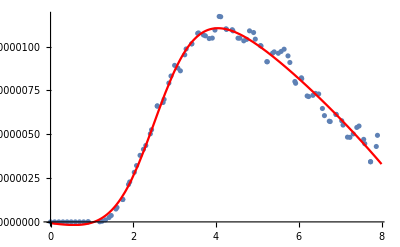

```mathematica
func = (a0+a1 q2+a2 q2^2+a4 q2^4)/((√q2-M0^2)^2+G^2);
model = NonlinearModelFit[rhoT[mode]⟦1⟧, func,{a0, a1, a2, a4, M0, G},q2];
Show[
PlotHST[rhoT[mode], PlotRange->All],
Plot[model[q2], {q2, 0, 8}, PlotRange->All, PlotStyle->Red]
]
fitRhoT[mode]=model["BestFit"];
```

## Saving

```mathematica
DeleteFile["./mdat/rhoT.mdat"];
file = OpenWrite["./mdat/rhoT.mdat"];
WriteString[file, ToString[Definition[rhoT], InputForm]<>"\n"];
WriteString[file, ToString[Definition[fitRhoT], InputForm]<>"\n"];
Close[file];
```